```mathematica
(* functionals forms *)
(* ****************************************************************)
(* epc17 *)
a17=2.35;
b17=2.4;
c171=3.2;
c172=6.6;
vepc171[re_]:=(-2 a17 denP[re]+b17 √denE[re] denP[re]^(3/2))/(2 (a17-b17 √denE[re] √denP[re]+c171 denE[re] denP[re])^2);
vepc172[re_]:=(-2 a17 denP[re]+b17 √denE[re] denP[re]^(3/2))/(2 (a17-b17 √denE[re] √denP[re]+c172 denE[re] denP[re])^2);

(* epc181*)
a181=1.8;
b181=0.1;
c181=0.03;
vepc181[re_]:=((-a181+c181 (denE[re]^(1/3)-denP[re]^(1/3)) (denE[re]^(1/3)+denP[re]^(1/3))^5+b181 (denE[re]^(1/3)+denP[re]^(1/3))^2 denP[re]^(1/3)) denP[re])/(a181+(-b181+c181 (denE[re]^(1/3)+denP[re]^(1/3))^3) (denE[re]^(1/3)+denP[re]^(1/3))^3)^2;

(* epc182*)
a182=3.9;
b182=0.5;
c182=0.06;
vepc182[re_]:=((-a182+c182 (denE[re]^(1/3)-denP[re]^(1/3)) (denE[re]^(1/3)+denP[re]^(1/3))^5+b182 (denE[re]^(1/3)+denP[re]^(1/3))^2 denP[re]^(1/3)) denP[re])/(a182+(-b182+c182 (denE[re]^(1/3)+denP[re]^(1/3))^3) (denE[re]^(1/3)+denP[re]^(1/3))^3)^2;

(* eμc *)
veμco[re_]:=((-2+√denP[re]) denP[re])/(1+4 denE[re] (2+√denP[re]) denP[re])^2;

veμcc[re_]:=((-2+√denP[re]) denP[re])/(1+2 denE[re] (2+√denP[re]) denP[re])^2;
```

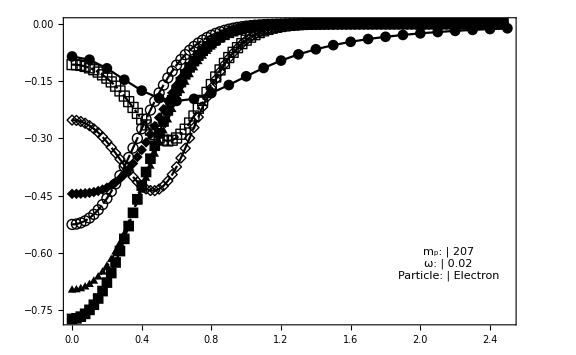

```mathematica
(* **************************************************** electron in mp=207*)
Clear[vcmat,denE,denP,epc171mat,epc172mat,epc181mat,epc182mat,eμcomat,eμccmat,start,end,npoints,step];
SetDirectory[NotebookDirectory[]];
vcmat=ToExpression[Import["VARdataCORR_E_207.txt","Lines"]];

mp=207;
ω=0.02;
me=1;
M=mp+me;
γ=1/2*M*ω;

SetDirectory["bestfit"];
denE[re_]=ToExpression[Import["fit6_fun_207_1_0.02_5.txt"]];
denP[rp_]=((2 √2 γ^(3/2))/π^(3/2)*ⅇ^(-2 rp^2 γ));

(* tables *)
start=10^-10;
end=2.5;
npoints=100;
step=end/npoints;

epc171mat=Table[{re,vepc171[re]},{re,start,end,step}];
epc172mat=Table[{re,vepc172[re]},{re,start,end,step}];
epc181mat=Table[{re,vepc181[re]},{re,start,end,step}];
epc182mat=Table[{re,vepc182[re]},{re,start,end,step}];
eμcomat=Table[{re,veμco[re]},{re,start,end,step}];
eμccmat=Table[{re,veμcc[re]},{re,start,end,step}];

nn=TableForm[{{"m_p:","207"},{"ω:","0.02"},{"Particle:","Electron"}}];
plot1=ListLinePlot[{vcmat[[1;;26]],epc171mat,epc172mat,epc181mat,epc182mat,eμcomat,eμccmat},PlotRange->All,Epilog->Inset[Framed[nn],Scaled[{0.85,0.2}]],PlotMarkers->{{"●",10.96},{"■",10.96},{"◆",10.88},{"▲",10.24},{"○",10.24},{"□",10.24},{"◇",10.24},{"△",11.136}},Frame->True,ImageSize->Large,PlotTheme->"Monochrome"]
```

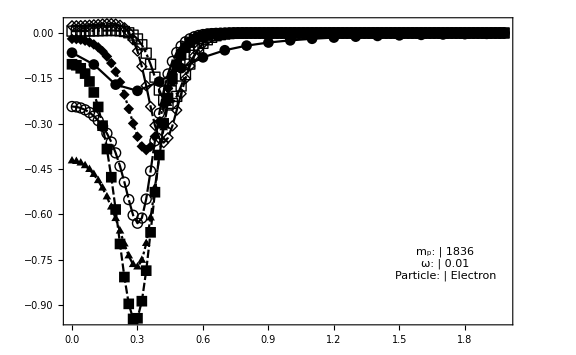

```mathematica
(* **************************************************** electron in mp=1836*)
Clear[vcmat,denE,denP,epc171mat,epc172mat,epc181mat,epc182mat,eμcomat,eμccmat,start,end,npoints,step];
SetDirectory[NotebookDirectory[]];
vcmat=ToExpression[Import["VARdataCORR_E_1836.txt","Lines"]];

mp=1836;
ω=0.01;
me=1;
M=mp+me;
γ=1/2*M*ω;

SetDirectory["bestfit"];
denE[re_]=ToExpression[Import["fit6_fun_1836_1_0.01_5.txt"]];
denP[rp_]=((2 √2 γ^(3/2))/π^(3/2)*ⅇ^(-2 rp^2 γ));

(* tables *)
start=10^-10;
end=2;
npoints=100;
step=end/npoints;

epc171mat=Table[{re,vepc171[re]},{re,start,end,step}];
epc172mat=Table[{re,vepc172[re]},{re,start,end,step}];
epc181mat=Table[{re,vepc181[re]},{re,start,end,step}];
epc182mat=Table[{re,vepc182[re]},{re,start,end,step}];
eμcomat=Table[{re,veμco[re]},{re,start,end,step}];
eμccmat=Table[{re,veμcc[re]},{re,start,end,step}];

nn=TableForm[{{"m_p:","1836"},{"ω:","0.01"},{"Particle:","Electron"}}];
plot2=ListLinePlot[{vcmat[[1;;20]],epc171mat,epc172mat,epc181mat,epc182mat,eμcomat,eμccmat},PlotRange->All,Epilog->Inset[Framed[nn],Scaled[{0.85,0.2}]],PlotMarkers->{{"●",10.96},{"■",10.96},{"◆",10.88},{"▲",10.24},{"○",10.24},{"□",10.24},{"◇",10.24},{"△",11.136}},Frame->True,ImageSize->Large,PlotTheme->"Monochrome"]
```

```mathematica
vcmat[[26]]
```

{2.5,0.000424215}

```mathematica
(**************************************************************************************************************)



(* functionals forms *)
(* ****************************************************************)
(* epc17 *)
a17=2.35;
b17=2.4;
c171=3.2;
c172=6.6;

vepc171P[rp_]=-(ρe[rp] (-b17 ρe[rp] ρn[rp]+2 a17 √(ρe[rp] ρn[rp])))/(2 √(ρe[rp] ρn[rp]) (a17+c171 ρe[rp] ρn[rp]-b17 √(ρe[rp] ρn[rp]))^2);
vepc172P[rp_]=-(ρe[rp] (-b17 ρe[rp] ρn[rp]+2 a17 √(ρe[rp] ρn[rp])))/(2 √(ρe[rp] ρn[rp]) (a17+c172 ρe[rp] ρn[rp]-b17 √(ρe[rp] ρn[rp]))^2);

(* epc181*************************************************************************************)
a181=1.8;
b181=0.1;
c181=0.03;

vepc181P[rp_]=-((ρe[rp] (a181-b181 ρe[rp]+c181 ρe[rp]^2-2 b181 ρe[rp]^(2/3) ρn[rp]^(1/3)+4 c181 ρe[rp]^(5/3) ρn[rp]^(1/3)-b181 ρe[rp]^(1/3) ρn[rp]^(2/3)+5 c181 ρe[rp]^(4/3) ρn[rp]^(2/3)-5 c181 ρe[rp]^(2/3) ρn[rp]^(4/3)-4 c181 ρe[rp]^(1/3) ρn[rp]^(5/3)-c181 ρn[rp]^2))/(a181-b181 ρe[rp]+c181 ρe[rp]^2-3 b181 ρe[rp]^(2/3) ρn[rp]^(1/3)+6 c181 ρe[rp]^(5/3) ρn[rp]^(1/3)-3 b181 ρe[rp]^(1/3) ρn[rp]^(2/3)+15 c181 ρe[rp]^(4/3) ρn[rp]^(2/3)-b181 ρn[rp]+20 c181 ρe[rp] ρn[rp]+15 c181 ρe[rp]^(2/3) ρn[rp]^(4/3)+6 c181 ρe[rp]^(1/3) ρn[rp]^(5/3)+c181 ρn[rp]^2)^2);

(* epc182 **************************************************************************)
a182=3.9;
b182=0.5;
c182=0.06;

vepc182P[rp_]=-((ρe[rp] (a182-b182 ρe[rp]+c182 ρe[rp]^2-2 b182 ρe[rp]^(2/3) ρn[rp]^(1/3)+4 c182 ρe[rp]^(5/3) ρn[rp]^(1/3)-b182 ρe[rp]^(1/3) ρn[rp]^(2/3)+5 c182 ρe[rp]^(4/3) ρn[rp]^(2/3)-5 c182 ρe[rp]^(2/3) ρn[rp]^(4/3)-4 c182 ρe[rp]^(1/3) ρn[rp]^(5/3)-c182 ρn[rp]^2))/(a182-b182 ρe[rp]+c182 ρe[rp]^2-3 b182 ρe[rp]^(2/3) ρn[rp]^(1/3)+6 c182 ρe[rp]^(5/3) ρn[rp]^(1/3)-3 b182 ρe[rp]^(1/3) ρn[rp]^(2/3)+15 c182 ρe[rp]^(4/3) ρn[rp]^(2/3)-b182 ρn[rp]+20 c182 ρe[rp] ρn[rp]+15 c182 ρe[rp]^(2/3) ρn[rp]^(4/3)+6 c182 ρe[rp]^(1/3) ρn[rp]^(5/3)+c182 ρn[rp]^2)^2);

veμcoP[rp_]=-(ρe[rp] (4-3 √ρn[rp]-16 ρe[rp] ρn[rp]^(3/2)))/(2 (1+4 ρe[rp] (2+√ρn[rp]) ρn[rp])^2);

veμccP[rp_]=-(ρe[rp] (4-3 √ρn[rp]-8 ρe[rp] ρn[rp]^(3/2)))/(2 (1+2 ρe[rp] (2+√ρn[rp]) ρn[rp])^2);
```

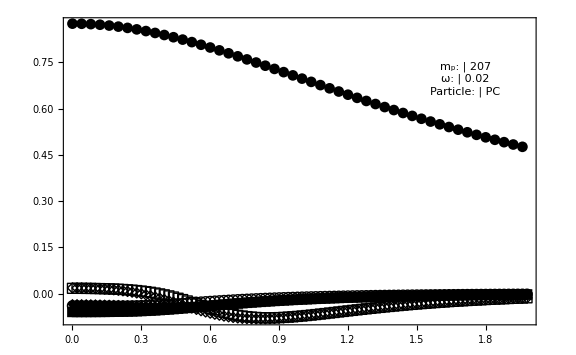

```mathematica
(* **************************************************** PC in mp=207*)
Clear[vcmat,ρe,ρn,epc171mat,epc172mat,epc181mat,epc182mat,eμcomat,eμccmat,start,end,npoints,step];
SetDirectory[NotebookDirectory[]];
vcmat=ToExpression[Import["VARdataCORR_P_207.txt","Lines"]];

mp=207;
ω=0.02;
me=1;
M=mp+me;
γ=1/2*M*ω;

SetDirectory["bestfit"];
ρe[re_]=ToExpression[Import["fit6_fun_207_1_0.02_5.txt"]];
ρn[rp_]=((2 √2 γ^(3/2))/π^(3/2)*ⅇ^(-2 rp^2 γ));

(* tables *)
start=10^-10;
end=2;
npoints=100;
step=end/npoints;

epc171mat=Table[{re,vepc171P[re]},{re,start,end,step}];
epc172mat=Table[{re,vepc172P[re]},{re,start,end,step}];
epc181mat=Table[{re,vepc181P[re]},{re,start,end,step}];
epc182mat=Table[{re,vepc182P[re]},{re,start,end,step}];
eμcomat=Table[{re,veμcoP[re]},{re,start,end,step}];
eμccmat=Table[{re,veμccP[re]},{re,start,end,step}];

nn=TableForm[{{"m_p:","207"},{"ω:","0.02"},{"Particle:","PC"}}];
plot3=ListPlot[{vcmat,epc171mat,epc172mat,epc181mat,epc182mat,eμcomat,eμccmat},PlotRange->All,Epilog->Inset[Framed[nn],Scaled[{0.85,0.8}]],PlotMarkers->{{"●",10.96},{"■",10.96},{"◆",10.88},{"▲",10.24},{"○",10.24},{"□",10.24},{"◇",10.24},{"△",11.136}},Frame->True,ImageSize->Large,PlotTheme->"Monochrome"]
```

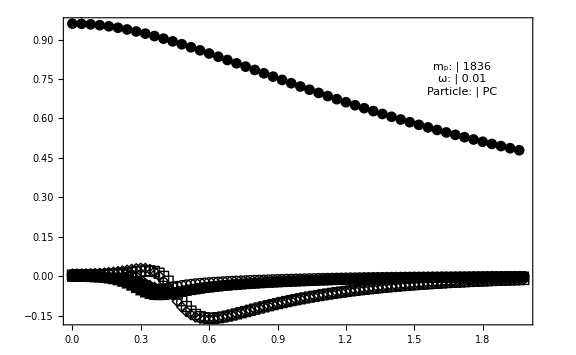

```mathematica
(* **************************************************** PC in mp=1836*)
Clear[vcmat,ρe,ρn,epc171mat,epc172mat,epc181mat,epc182mat,eμcomat,eμccmat,start,end,npoints,step];
SetDirectory[NotebookDirectory[]];
vcmat=ToExpression[Import["VARdataCORR_P_1836.txt","Lines"]];

mp=1836;
ω=0.01;
me=1;
M=mp+me;
γ=1/2*M*ω;

SetDirectory["bestfit"];
ρe[re_]=ToExpression[Import["fit6_fun_1836_1_0.01_5.txt"]];
ρn[rp_]=((2 √2 γ^(3/2))/π^(3/2)*ⅇ^(-2 rp^2 γ));

(* tables *)
start=10^-10;
end=2;
npoints=100;
step=end/npoints;

epc171mat=Table[{re,vepc171P[re]},{re,start,end,step}];
epc172mat=Table[{re,vepc172P[re]},{re,start,end,step}];
epc181mat=Table[{re,vepc181P[re]},{re,start,end,step}];
epc182mat=Table[{re,vepc182P[re]},{re,start,end,step}];
eμcomat=Table[{re,veμcoP[re]},{re,start,end,step}];
eμccmat=Table[{re,veμccP[re]},{re,start,end,step}];

nn=TableForm[{{"m_p:","1836"},{"ω:","0.01"},{"Particle:","PC"}}];
plot4=ListPlot[{vcmat,epc171mat,epc172mat,epc181mat,epc182mat,eμcomat,eμccmat},PlotRange->All,Epilog->Inset[Framed[nn],Scaled[{0.85,0.8}]],PlotMarkers->{{"●",10.96},{"■",10.96},{"◆",10.88},{"▲",10.24},{"○",10.24},{"□",10.24},{"◇",10.24},{"△",11.136}},Frame->True,ImageSize->Large,PlotTheme->"Monochrome"]
```

```mathematica
(*PlotLegends->{"exact","epc17-1","epc17-2","epc18-1","epc18-2","eμc (open shell)","eμc (closed shell)"}*)
```

```mathematica
leg=PointLegend[{Directive[PointSize[0.0055000000000000005],CapForm["Butt"],AbsoluteThickness[1.6],AbsoluteDashing[{}],Black],Directive[PointSize[0.0055000000000000005],CapForm["Butt"],AbsoluteThickness[1.6],AbsoluteDashing[{6,2}],Black],Directive[PointSize[0.0055000000000000005],CapForm["Butt"],AbsoluteThickness[1.6],AbsoluteDashing[{2,2}],Black],Directive[PointSize[0.0055000000000000005],CapForm["Butt"],AbsoluteThickness[1.6],AbsoluteDashing[{6,2,2,2}],Black],Directive[PointSize[0.0055000000000000005],CapForm["Butt"],AbsoluteThickness[1.6],AbsoluteDashing[{12,2}],Black],Directive[PointSize[0.0055000000000000005],CapForm["Butt"],AbsoluteThickness[1.6],AbsoluteDashing[{12,2,2,2,2,2}],Black],Directive[PointSize[0.0055000000000000005],CapForm["Butt"],AbsoluteThickness[1.6],AbsoluteDashing[{24,2,8,2}],Black]},{"exact","epc17-1","epc17-2","epc18-1","epc18-2","eμc (open shell)","eμc (closed shell)"},LegendMarkers->{{"●",10.96},{"■",10.96},{"◆",10.88},{"▲",10.24},{"○",10.24},{"□",10.24},{"◇",10.24}},Joined->{False,False,False,False,False,False,False},LegendLayout->"Row",LabelStyle->Black,ImageSize->{600,40}]
```

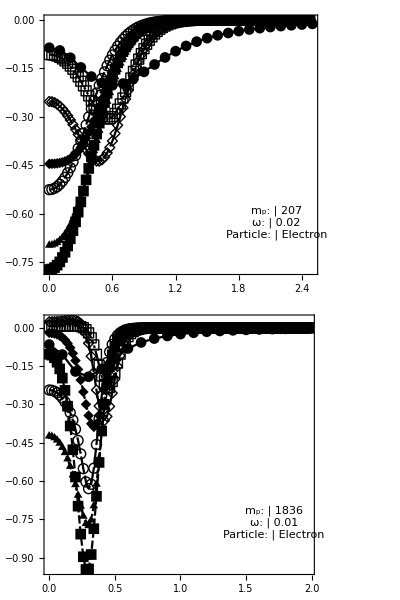

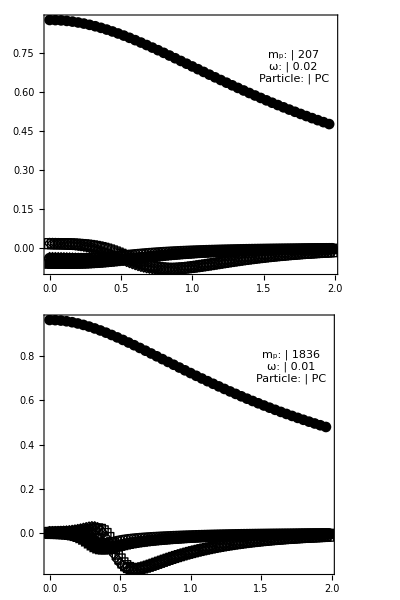

```mathematica
grid01=Grid[{{plot1},{plot2}}];
grid02=Grid[{{plot3},{plot4}}];
grid11=Grid[{{grid01},{leg}},Alignment->Center]
grid22=Grid[{{grid02},{leg}},Alignment->Center]
```

```mathematica
Export["grid_E_FUNC.png",grid11]
Export["grid_P_FUNC.png",grid22]
```

grid_E_FUNC.png

grid_P_FUNC.png